# CODE DOCUMENT

## Implementation

Due to the undecidability of universal static analysis and the computational irreducibility of Turing machine evolution, the implementation will inevitably be brute-force in nature. However, there are certain ways to prune the search space by examining only the rules. There are also optimizations for Turing machine simulation, particularly with memoizing sections of the tape.

### Pruning

Despite the undecidability of finding a universal way of reducing computation across Turing machines or even on one Turing machine, we can take inspiration from DFA (deterministic finite automaton) minimization. Specifically, one big optimization we can make is to declare that all Turing machines with rules that permute a dead state (unreachable from the initial state) to be equal: each of these permutations are unreachable anyway.

The diagram below shows two equivalent Turing machines, each with a different permutation of the rules from state 2, which is unreachable from state 1.

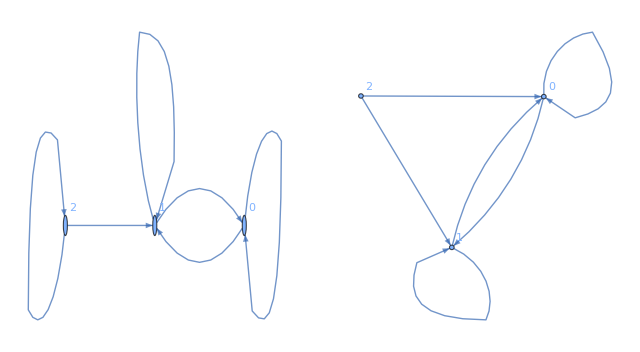

```mathematica
GraphicsRow[{
Graph[{1->1,1->0,0->1,0->0,2->1,2->2},VertexLabels->Automatic],
Graph[{1->1,1->0,0->1,0->0,2->0,2->1},VertexLabels->Automatic]
}]
```

Determining the reachable nodes is simply graph traversal. It is not hard to see that all state graphs have  vertices and  edges, resulting in a runtime of .

The numbering system of Turing machines in the Wolfram Language permutes rules in the following order: direction (-1 to 1), symbol (0 to ), then state (1 to ). For the rest of the essay, we will use this numbering without loss of generality. Notice that for consecutive unreachable states ending in state  (e.g. 2, 3 for ), their rule numbers will also be grouped separately so we only need to define the interval (start and end) of rule numbers of an equivalence class. For example, suppose that state 3 is unreachable for . Then there exists contiguous intervals of rules that are isomorphic, such as rules 83520 to 84096. Thus, for each of these blocks, we can skip ahead to the end of a block when we encounter its beginning. Consequently, this is also the only time we can speed up iteration.

The length of an iteration depends on the number of reachable states. If there are  reachable states from 1 to , then there are  unreachable states. The number of ways we can permute these unreachable states is given by , since there are  symbols per state and  ways to permute each single component of a rule.

Set number of states and symbols:

```mathematica
states=3;
symbols=3;
machines=(2*states*symbols)^(states*symbols);
machines=206000000;
```

getinfo requires the full form of a rule, but rule numbers are easier to comprehend, so we will use the following two resource functions to convert between them.

Resource functions to convert between rule full form and rule number:

```mathematica
tmRuleFromNum=ResourceFunction["TuringMachineFromNumber"];
tmRuleToNum=ResourceFunction["TuringMachineToNumber"];
```

Gets a rule’s hash map key and generate a state diagram from the rule:

```mathematica
getinfo[r_]:={r[[All,2]],Graph[r[[All,All,1]]]}
```

The key construction will be to point all unreachable states to 1’s so that they map to the beginning of an equivalent block of rules if the condition is satisfied. The following function gets this key and the state graph of a machine.

Transforms a return value from getinfo into a hash key such that all equivalent Turing machines have the same key:

```mathematica
cftransform=
FunctionCompile[
Function[
{
Typed[states,"MachineInteger"],
Typed[symbols,"MachineInteger"],
Typed[reachable,"PackedArray"::["MachineInteger",1]],
Typed[key,"PackedArray"::["MachineInteger",1]]
},
Flatten@
Table[
If[
MemberQ[reachable,j],
Flatten@Table[key[[k]],{k,3*symbols(j-1)+1,3*symbols*j}],
Table[1,3*symbols]
],
{j,states}
]
]
];
```

$Aborted

```mathematica
tmRuleFromNum[0,states,symbols]
getinfo[%]
cftransform[states,symbols,{1},Flatten@%[[1]]]
```

Returns :

```mathematica
perm[d_Integer]:=(2*states*symbols)^(symbols*(states-d))
```

Checks if l is a consecutive list that starts with 1:

```mathematica
consQ[l:{___Integer}]:=First[l]==1&&Most[l]+1===Rest[l]
consQ[_List]:=False
```

Counts of the number of Turing machines that map to the same key (are equal):

```mathematica
map=CreateDataStructure["HashTable"];
```

TODO: OPTIMIZEEEEE

```mathematica
prunefor[len_Integer]:=
Module[{rcur,tmp,i},
For[
i=CreateDataStructure["Counter",0],
i["Get"]<len,
i["Increment"],
With[{info=getinfo[tmRuleFromNum[i["Get"],states,symbols]]},
rcur=VertexOutComponent[info[[2]],1];
map[
"Insert",
(#->map["Lookup",#,0&]
+If[
consQ[Sort[rcur]],
tmp=perm[Length[rcur]];i["AddTo",tmp-1];tmp,
1
]
)&@cftransform[states,symbols,rcur,Flatten@info[[1]]]
];
]
]
]
```

```mathematica
map=CreateDataStructure["HashTable"];
prunefor[1000000];//AbsoluteTiming
map["Elements"];
```

Takes in the number of rules to analyze from 0 to len-1 and loops through those rules, skipping if possible.

```mathematica
prune[len_Integer]:=
Module[{rcur,tmp,cnt=CreateDataStructure["Counter",0]},
ResourceFunction["MonitorProgress"]@
Do[
If[
cnt["Get"]>0,
cnt["Decrement"],
With[{info=getinfo[tmRuleFromNum[i,states,symbols]]},
rcur=VertexOutComponent[info[[2]],1];
map[
"Insert",
(*({#,i}->map["Lookup",{#,i},0&]*)
(#->map["Lookup",#,0&]
+If[
consQ[Sort[rcur]],
tmp=perm[Length[rcur]];cnt["Set",tmp-1];tmp,
1
]
)&@cftransform[states,symbols,rcur,Flatten@info[[1]]]
];
]
],
{i,0,len-1}
]
]
map=CreateDataStructure["HashTable"];
prunefor[512]
map["Elements"][[1;;2]]
```

Part::take: Cannot take positions 1 through 2 in {{1,0,-1,1,0,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}→16777216}.

{{1,0,-1,1,0,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}→16777216}⟦1;;2⟧

Call the function: START RUN HERE

```mathematica
map=CreateDataStructure["HashTable"];
prunefor[machines];
elems=map["Elements"];
```

We can confirm that equivalence classes (not just those that are consecutive) come in sizes of  for all nonnegative : for , we indeed have , , .

```mathematica
DeleteDuplicates[elems[[All,2]]]
```

{1,5832,34012224}

### Rule Extraction

Now we will convert the rules back to their canonical numbered form for ease of analysis.

Number of times each rule repeats:

```mathematica
ruleRepeats:=elems[[All,2]];
```

Reconstruct full form rules:

```mathematica
fullRules=With[
{
key=Transpose@{
Flatten@Table[ConstantArray[i,symbols],{i,states}],
Table[Mod[i,symbols],{i,states*symbols-1,0,-1}]
},
vals=Partition[#[[1]],3]&/@elems
},
ParallelMap[Table[key[[i]]->#[[i]],{i,states*symbols}]&,vals]
];
```

Convert full form rules to numbered rules:

```mathematica
ruleNumsCompressed=(*ResourceFunction["MonitorProgress"]@*)tmRuleToNum[#][[1]]&/@fullRules;
```

```mathematica
fullRules=.
```

### Search

As mentioned, the behavior or a Turing machine is undecidable even on a finite tape. Thus, we find optimization in our simulation implementation. One notable bottleneck—amongst others—are repeating and non-terminating states. Naturally, we can solve this using dynamic programming.

```mathematica
dprad=8;
width=64;
bits=4;
```

```mathematica
stepTM[rule_Integer,stages_List,blockwidth_Integer]:=
With[
{tms=TuringMachine[{rule,states,symbols},stages[[-1]],blockwidth]},
Transpose@{
tms[[All,1]],
PadLeft[#[[2]],width,0,(*tms[[1,1,2]]*)width-Length[#[[2]]]]&/@tms
}
]
```

```mathematica
htDP[rule_Integer,bits_Integer,blockwidth_Integer,maxdepth_Integer]:=
Transpose@
With[{dpG=CreateDataStructure["LeastRecentlyUsedCache",256]},
Table[
Module[
{
dp=CreateDataStructure["LeastRecentlyUsedCache",256],
i=CreateDataStructure["Counter",1],
cnt=CreateDataStructure["Counter",0],
tms,tmp,
flag=False,
cur={{0,0,0}}
},
(*Print[n];*)
(*Print["======"];*)
tms=NestWhile[
stepTM[rule,#,blockwidth]&,
stepTM[rule,{{{1,width,0},{IntegerDigits[n,2,width],0}}},blockwidth],
(
(*tm=Transpose@{
#[[All,1]],
PadLeft[#[[2]],width,0,width-Length[#[[2]]]]&/@#
};*)
(*Print[tm];*)
(*Print[#[[All,1]]];
Print["------"];*)
i["Set",1];
While[
cur=#[[i["Get"]]];
(*Print[cur];*)
i["Get"]<=blockwidth&&!flag&&(*1-width<=*)cur[[1,3]]<=0,

(*Print[{i["Get"],cnt["Get"],cur}];*)
tmp=Join[
{cur[[1,1]],cur[[1,3]]},
PadLeft[cur[[2]],2*dprad-1,0,dprad+cur[[1,3]]-1]
];
(*Print[tmp];*)
If[
!(flag=dpG["KeyExistsQ",tmp]),
If[
(flag=dp["KeyExistsQ",tmp]),
dpG["Insert",tmp->1],
dp["Insert",tmp->1]
]
];
(*Print[{i["Get"],flag,cur[[1,3]]}];*)
i["Increment"];
cnt["Increment"];
];
i["Get"]==blockwidth+1&&!flag&&(*1-width<=*)cur[[1,3]]<=0
)&,
1,maxdepth
];
Flatten[{
If[flag||cnt["Get"]==maxdepth*blockwidth,-1,cnt["Get"]],
If[tms[[i["Get"],1,3]]==1,FromDigits[tms[[i["Get"],2]],2],-1]
}]
],
{n,0,2^bits-1}
(*{n,15,15}*)
]
]
chtDP[1447,4,4,32]
```

chtDP[1447,4,4,32]

```mathematica
init[n_]:={{1,width},{IntegerDigits[n,2,width],0}}
```

```mathematica
chtDP=
Compile[
{
{rule,_Integer},
{bits,_Integer},
{blockwidth,_Integer},
{maxdepth,_Integer}
},
htDP[rule,bits,blockwidth,maxdepth],
{{htDP[___],_Integer,2}},
CompilationTarget->"C",
CompilationOptions->{"InlineExternalDefinitions" -> True},
RuntimeOptions->"Speed",
RuntimeAttributes->{Listable}
];
```

```mathematica
halts=ParallelMap[htDP[#,4,4,16]&,ruleNumsCompressed];
```

{rule, # times repeated, {halt times}, {halt values}}

```mathematica
haltconfig=Transpose@{
ruleNumsCompressed,
elems[[All,2]],
halts[[All,1]],
halts[[All,2]]
};
```

```mathematica
halts=.
```

```mathematica
Export["./wsrp/project/main/mx/33/33_haltconfig.mx",haltconfig,"MX"];
```

{{range, min, max, rules...}...}

```mathematica
haltgroups=(*ResourceFunction["MonitorProgress"]@*)Map[
With[{ttl=Total[#[[All,2]]],mm=MinMax[Max[#[[3]]]&/@#]},
Flatten@{mm[[2]]-mm[[1]],mm,#[[All,1]]}
]&,
GatherBy[
Select[haltconfig,!ContainsOnly[#[[3]],{-1}]&],
#[[4]]&(*#[[4]] can be all -1 if htDP hits it max depth*)
]
];
Length@%
```

17451

```mathematica
Export["./wsrp/project/main/mx/33/33_haltgroups.mx",haltgroups,"MX"];
```

```mathematica
CloudPut[haltgroups](*new cloud object for 22*)
```

CloudObject[https://www.wolframcloud.com/obj/1e1e1e10-681c-4346-b486-2ec3b138be09]

TODO: run when done

```mathematica
haltgroups33=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/1e1e1e10-681c-4346-b486-2ec3b138be09"](https://www.wolframcloud.com/obj/1e1e1e10-681c-4346-b486-2ec3b138be09)]];
```

```mathematica
genplot[data_List]:=
With[
{
sup=Length@data,
sizsup=Max[Length/@data]-3,
step=IntegerPart[Length@data/400],
sizstep=IntegerPart[Max[Length/@data]/400]
},
Manipulate[
With[{
w=1000,
sorted=SortBy[
data,Switch[
sort,
"Runtime Range",-First[#]&,
"Class Size",-Length[#]&,
"Max Runtime",-#[[3]]&,
"Min Runtime",-#[[2]]&
]
]
},
Column[{
ListPlot[
((Length/@sorted)-3)[[Min[a,b];;b]],
Joined->True,
PlotRange->{{Automatic,Automatic},{Automatic,sizbound}},
ImageSize->{w,Automatic},
AspectRatio->1/16,
PlotLabel->"Equivalence Class Size"
],
ListPlot[
(First/@sorted)[[Min[a,b];;b]],
Joined->True,
PlotRange->All,
ImageSize->{w,Automatic},
AspectRatio->1/10,
PlotLabel->"Runtime Range"
],
ListPlot[
{sorted[[All,2]][[Min[a,b];;b]],sorted[[All,3]][[Min[a,b];;b]]},
Joined->True,
PlotRange->All,
ImageSize->{w,Automatic},
AspectRatio->1/6,
PlotLabel->"Maximum and Minimum Runtime",
PlotLegends->{"Min","Max"}
]
}]
],
{{a,1,"Left bound"},1,sup,step,Appearance->"Labeled"},
{{b,sup,"Right bound"},1,sup,step,Appearance->"Labeled"},
{{sort,"Runtime Range","Sort by"},{"Runtime Range","Class Size","Max Runtime","Min Runtime"}},
{{sizbound,sizsup,"Size upper bound"},50,sizsup,sizstep,Appearance->"Labeled"},
SaveDefinitions->True
]
]
```

```mathematica
genplot[haltgroups33]
```

## Existing Work

We will begin by recreating the results shown on page 761 of Stephen Wolfram’s A New Kind of Science. Wolfram found that the space of all 2-state 2-color Turing machines represents exactly 351 distinct functions.

We will first create a function that simulates the evolution of a Turing machine with a tape set to some  with rule  until it reaches a halt state. Wolfram set the halt state as when the head to move to the right of its starting position (where the digits are not defined). Clearly, not all Turing machines will halt, so we will need to set a maximum iteration count. Also, for now, only four bit numbers will be used, which can represent numbers from 0 to 15.

Initialize rules and max iteration count:

```mathematica
states=2;
colors=2;
maxiters=64;
rules=Range[0,(2*states*colors)^(states*colors)-1];
bits=4;
width=11;
```

Using a smaller width allows less buffer space for the Turing machine to move past our defined interval  to give it a chance to return to . Wolfram used a width of 11 in NKS and I will use the smallest width possible of bits, which if 4. This is why our results diverge slightly. Note that results will be the same for width  6.

```mathematica
Length[rules]
```

4096

Why 4096 rules? For a -state -color Turing machine, there are  possible transitions, and for each transition there are  states to move to,  colors to change to, and 2 directions to move in, which results in a total of  machines. For , we have . This is why a generalized solution is difficult. For each increase of , the number of Turing machines increases exponentially by a factor of itself: enumeration is .

We set the initial condition to start in state 1 at position 11 of a tape of length 11 containing the value .

Set the initial condition as a function of :

```mathematica
init[n_]:={{1,width},{IntegerDigits[n,2,width],0}}
```

The Block body loops through the Turing machine evolution and checks for termination, which is passed to a Transpose block that trims the tape to only contain the first 11 colors. Since it loops through each stage of a Turing machine, it runs in approximately maxiters^2 time.

Stepping through the Turing machine evolution at every step is slower than generating it all at once even though there’s more symbols generated on average???

```mathematica
trim[stages_List,width_Integer]:=
Module[
{min=Min[stages[[All,2]],stages[[1,2]]-width]-1,head,tail},
head=(#-{0,min,0})&/@stages[[All,1;;3]];
tail=ArrayPad[
stages[[All,4;;-1]],
{{0,0},{-min,stages[[1,2]]-(Length[stages[[1]]]-3)-stages[[1,3]]}}
];
Join[head[[#]],tail[[#]]]&/@Range[Length[head]]
]
```

Compiled function to include and trim states until halt:

```mathematica
cfindhalt=Compile[
{{evols,_Integer,2},{width,_Integer}},
Module[{min=Min[#[[All,2]],#[[1,2]]-width]-1,head,tail},
head=(#-{0,min,0})&/@#[[All,1;;3]];
tail=ArrayPad[
#[[All,4;;-1]],
{{0,0},{-min,#[[1,2]]-(Length[#[[1]]]-3)-#[[1,3]]}}
];
Join[head[[#]],tail[[#]]]&/@Range[Length[head]]
]&[
Module[{halt=False},
TakeWhile[
evols,
Which[
halt,
False,
(*1-width<=*)#[[3]]<=0,(* valid position *)
True,
MatchQ[#[[3]],1(*|-width*)],(* halt position *)
halt=True
]&
]
]
],
{{trim[_],_Integer,2}},
CompilationTarget->"C",
RuntimeAttributes->{Listable}
];
```

Compiled hist function:

```mathematica
chist[rule_Integer, num_Integer]:=
cfindhalt[
Flatten/@TuringMachine[{rule,states,colors},init[num],maxiters],width
]
```

Example for rule 2237 starting on a tape of all zeros ().

```mathematica
Grid[
{#[[1;;3]],#[[4;;-1]]}&/@chist[2237,3],
Alignment->Left
]
```

{1,12,0} | {0,0,0,0,0,0,0,0,0,0,1,1}
{2,11,-1} | {0,0,0,0,0,0,0,0,0,0,1,0}
{2,12,0} | {0,0,0,0,0,0,0,0,0,0,1,0}
{2,13,1} | {0,0,0,0,0,0,0,0,0,0,1,0}

Now that we can get the full evolution of a Turing machine, we want to see the final result on termination for each of these machines. The function is shown below, which loops through each rule, then each number constrained by bits bits, and returning the final tape.

Get the final stage of evolution for each rule and number:

```mathematica
getevols[rules_List,bits_Integer]:=
ParallelMap[
Join[{
#,
Table[
With[{h=chist[#,num]},
If[
h[[-1,3]]!=1,
-1,
FromDigits[h[[-1,4;;-1]],2]
]
],(* end With *)
{num,0,2^bits-1}
](* end Table over 2^bits-1 *)
}]&,(*end Join *)
rules
];(* end Table over r *)
```

Call the function:

```mathematica
evols=getevols[rules,bits];
%[[2238]] (* final state of rule 2237 *)
```

{2237,{-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14}}

The following two functions separate Turing machine equivalence classes into different groups.

Group rules by equivalence class and filter out non-terminating machines:

```mathematica
eqlgroups=
Map[
First,
GatherBy[
Select[
Transpose[{rules,evols}],
!ContainsOnly[#[[2,2]],{-1}]&
],
#[[2,2]]&
],
{2}
];
```

Number of groups:

```mathematica
Length[eqlgroups]
```

350

Group rules as above and additionally filter out unique machines:

```mathematica
multieqlgroups=
Map[
First,
Select[
GatherBy[
Select[
Transpose[{rules,evols}],
!ContainsOnly[#[[2,2]],{-1}]&
],
#[[2,2]]&
],
Length[#]>1&
],
{2}
];
```

For analysis purposes, multieqlgroups is more useful since we cannot say much about a Turing machine that is unique in what it does.

To measure the time complexity of each Turing machine, we are forced to do a brute-force simulation due to the Halting Problem.

Simulate the number of transitions until halt for all numbers of bits bits:

```mathematica
ht[rule_Integer,bits_Integer]:=
Select[
ParallelTable[
Module[{i=0,max=maxiters+1},(* 50 + 2n *)
NestWhile[
(i++;TuringMachine[{rule,states,colors},#])&,
{{1,width,0},{IntegerDigits[n,2,width],0}},
(*1-width<=*)#[[1,3]]<=0&,(* stop when dx > 0, or when x < 1 - width *)
1,max
];
If[i==max,-1,i]
],
{n,0,2^bits-1}
],
#!=-1&
]
```

Halting configuration for rule 2238 for all 4 bit numbers:

```mathematica
ht[2237,bits]
```

{3,5,3,7,3,5,3,9,3,5,3,7,3,5,3}

To analyze the time complexity difference between each group of Turing machines, it is helpful to have explicit access to those values.

Get the 3-tuples for each group of Turing machines {min,max,range}

```mathematica
halttimes=Map[{#,ht[#,bits]}&,eqlgroups,{2}];
```

$Aborted

```mathematica
((Max@@#[[2]])&/@#)&/@halttimes; 
MinMax/@%;
haltdifs=Append[#,#[[2]]-#[[1]]]&/@%;
```

Combine each group into {tuple,{rules...},{{runtimes}...}}:

```mathematica
haltcombined=Transpose@{haltdifs,eqlgroups,halttimes[[All,All,2]]};
```

THIS DOES NOTHING WTF Sort by largest range: corresponding slow and fast Turing machines:

```mathematica
sortedmachines={#[[1]],Transpose[#[[2;;3]]]}&/@SortBy[haltcombined,-#[[1,-1]]&];
```

```mathematica
list=Transpose@{sortedmachines[[All,1]],sortedmachines[[All,2,All,1]]};
```

List of the number of Turing machines in each  equivalence class:

```mathematica
Length@#[[2]]&/@list
```

{280,273,19,3,119,4,6,119,6,5,6,2,2,3,5,5,8,99,2,5,99,2,6,2,5,2,2,3,4,8,9,3,5,6,9,6,261,269,4,4,6,6,8,8,9,9,11,11,12,12,14,14,19,19,3,2,2,4,4,4,17,2,3,4,4,4,17,226,226,232,232,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,8,8,11,11,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,3,3,3,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,3,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,3,3,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,8,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

### POTENTIALLY OUTDATED SECTION

The number of unique functions 351 we found here is the same number Wolfram found in NKS (Wolfram, 759).

Find the last group (it turns out) of size 17 and see the outputs:

```mathematica
Length@#[[2]]&/@list;
Position[%,17,-1][[2,1]];
If[%!=-1,evols[[list[[%,2,1]]+1,2]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

## Distribution Analysis

```mathematica
stackPoints[l_List]:=MapIndexed[Function[{value,index},{First@index,#}&/@value]]@l
```

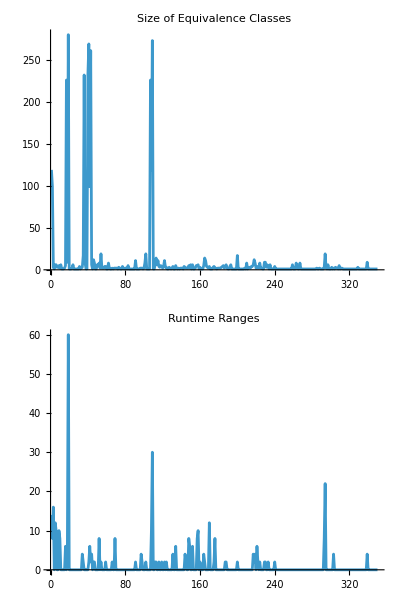

```mathematica
Column[
With[
{w=1600},
{
ListPlot[
Length/@eqlgroups,
PlotRange->All,
Joined->True,
ImageSize->{w,Automatic},
AspectRatio->1/16,
PlotLabel->"Size of Equivalence Classes"
],
ListPlot[
haltdifs[[All,3]],
PlotRange->All,
Joined->True,
ImageSize->{w,Automatic},
AspectRatio->1/16,
PlotLabel->"Runtime Ranges"
]
}
]
]
```

Generally, spikes in the size of equivalence classes, aside from the first, generally corresponds to spikes in runtime range, yet there are also some spikes where there is low runtime range.
Spikes in runtime ranges are more frequent. Some spikes correspond with large equivalence classes, but there is a spike at group 295 where the size is very small. Large runtime ranges also happen during the large size spike in the beginning.

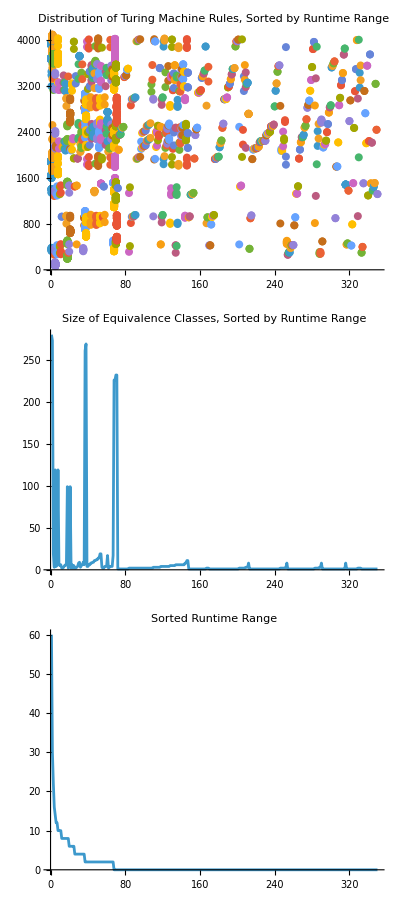

```mathematica
Column[
With[{w=1600},
{
ListPlot[
stackPoints[list[[All,2]]],
PlotRange->Full,
ImageSize->{w,Automatic},
AspectRatio->1/3,
PlotLabel->"Distribution of Turing Machine Rules, Sorted by Runtime Range"
],
ListPlot[
Length/@list[[All,2]],
PlotRange->All,
Joined->True,
ImageSize->{w,Automatic},
AspectRatio->1/16,
PlotLabel->"Size of Equivalence Classes, Sorted by Runtime Range"
],
ListPlot[
list[[All,1,3]],
PlotRange->All,
Joined->True,
ImageSize->{w,Automatic},
AspectRatio->1/8,
PlotLabel->"Sorted Runtime Range"
]
}
]
]
```

larger groups of isomorphic rules generally correspond to a larger difference so we only pick the large groups??

## Future Directions

stream algorithm?
analyze state diagram patterns to extend beyond dfa minimzation
optimize htdp for parallel cores by sacrificing total dp?? test performance
make dp better by extrapolating directions/skip steps